## K-states representation for the wave functions |IMK>

## Constants

```mathematica
angles={π/3,π/5,π/7};
spin=3;
```

## Wigner functions

```mathematica
wd[spin_,m_,k_,angles_]:=WignerD[{spin,m,k},angles[[1]],angles[[2]],angles[[3]]];
wdreal[spin_,m_,k_,angles_]:=Re[wd[spin,m,k,angles]];
```

```mathematica
Kstates[spin_,k_,angles_]:=Table[N[wdreal[spin,mi,k,angles]],{mi,-spin,spin,1}];
```

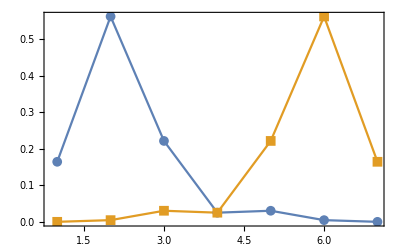

```mathematica
ListPlot[{Abs[Kstates[3,-3,angles]],Abs[Kstates[3,3,angles]]},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,PlotRange->All]
```